### Set up the code

```mathematica
qn[q1_,n_,α_]:=q1 (1-α)^(n-1)
```

```mathematica
pn[q1_,n_,α_]:=1-qn[q1,n,α]
```

```mathematica
p1=pn[q1,1,α]
```

1-q1

```mathematica
p2=pn[q1,2,α]
```

1-q1 (1-α)

```mathematica
Bin[n_,k_,p_]:=PDF[BinomialDistribution[n,p],k]
```

### Mean matrix

```mathematica
m11=FullSimplify[2 ∑_(i=0)^2 i Bin[2,i,p1]]
```

4-4 q1

```mathematica
m12=Expand[FullSimplify[Bin[2,1,p1]]]
```

2 q1-2 q1^2

```mathematica
m13=FullSimplify[Bin[2,2,p1]]
```

(-1+q1)^2

```mathematica
m21=FullSimplify[2 Bin[1,1,p2]]
```

2+2 q1 (-1+α)

```mathematica
m24=FullSimplify[∑_(i=0)^2 i Bin[1,i,p2]]
```

1+q1 (-1+α)

```mathematica
M={{m11,m12,m13,0},{m21,0,0,m24},{0,0,0,0},{0,0,0,0}}
```

{{4-4 q1,2 q1-2 q1^2,(-1+q1)^2,0},{2+2 q1 (-1+α),0,0,1+q1 (-1+α)},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[M]/.{q1->1-p}//FullSimplify
```

(4 p | -2 (-1+p) p | p^2 | 0
2 (p+α-p α) | 0 | 0 | p+α-p α
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[M]/.{q1->0.9,α-> 0.1}
```

(0.4 | 0.18 | 0.01 | 0
0.38 | 0 | 0 | 0.19
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Eigenvalues

```mathematica
FullSimplify[Eigenvalues[M,-1]]
```

{2 (1-q1+√(-((-1+q1) (1+q1^2 (-1+α)))))}

```mathematica
Eigenvalues[M]/.{q1->0.8,α->0.2}
```

{0,0,-0.22482,1.02482}

```mathematica
λmax=Eigenvalues[M]⟦4⟧
```

2 (1-q1+√(1-q1-q1^2+q1^3+q1^2 α-q1^3 α))

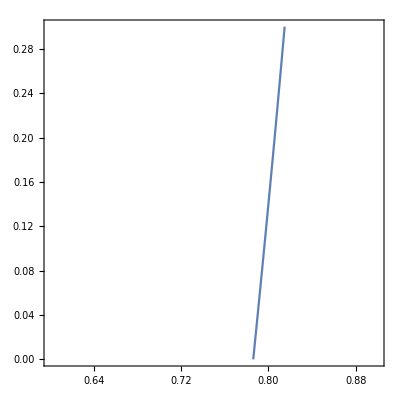

```mathematica
ContourPlot[{λmax==1,λmax2==1},{q1,0.6,0.9},{α,0,.3}]
```

```mathematica
λmax/.{q1->4/5}
```

2 (1/5+√(9/125+(16 α)/125))

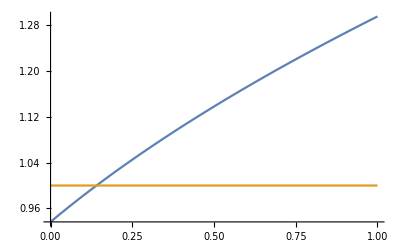

```mathematica
Plot[{λmax/.{q1->4/5},1},{α,0,1}]
```

```mathematica
Table[{α,λmax/.{q1->4/5}},{α,0.1,0.2,0.01}]
```

{{0.1,0.982409},{0.11,0.986788},{0.12,0.991135},{0.13,0.995449},{0.14,0.999733},{0.15,1.00399},{0.16,1.00821},{0.17,1.01241},{0.18,1.01657},{0.19,1.02071},{0.2,1.02482}}

```mathematica
eqn=Expand[λmax/.{q1->4/5}]
```

2/5+2 √(9/125+(16 α)/125)

```mathematica
TeXForm[eqn]
```

2 \sqrt{\frac{16 \alpha }{125}+\frac{9}{125}}+\frac{2}{5}

```mathematica
Solve[eqn==1,α]
```

{{α→9/64}}

```mathematica
N[{{α->9/64}}]
```

{{α→0.140625}}

```mathematica
9/64//TeXForm
```

\frac{9}{64}

```mathematica
M//MatrixForm
```

(4-4 q1 | 2 q1-2 q1^2 | (-1+q1)^2 | 0
2+2 q1 (-1+α) | 0 | 0 | 1+q1 (-1+α)
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ConstantArray[1,4]
```

{1,1,1,1}

```mathematica
LinearSolve[IdentityMatrix[4]-M,ConstantArray[1,4]][[1]]/.{q1->0.1,α->0.1}
```

-0.735688

```mathematica
LinearSolve[IdentityMatrix[4]-M,ConstantArray[1,4]][[1]]
```

(2+2 q1-5 q1^2+2 q1^3+2 q1^2 α-2 q1^3 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α)

```mathematica
MatrixPower[M,2][[1,1]]//Expand
```

16-28 q1+8 q1^2+4 q1^3+4 q1^2 α-4 q1^3 α

### Expected cascade size

```mathematica
M/.{α->0.1, q1->0.9}//MatrixForm
```

(0.4 | 0.18 | 0.01 | 0
0.38 | 0 | 0 | 0.19
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
a = {0,1,2,1}
```

{0,1,2,1}

```mathematica
x = {x1,x2,x3,x4}
```

{x1,x2,x3,x4}

```mathematica
x//MatrixForm
```

(x1
x2
x3
x4)

```mathematica
MI = Inverse[IdentityMatrix[4]- M]//FullSimplify
```

{{1/(-3+4 q1^2 (2+q1 (-1+α)-α)),-(2 (-1+q1) q1)/(-3+4 q1^2 (2+q1 (-1+α)-α)),(-1+q1)^2/(-3+4 q1^2 (2+q1 (-1+α)-α)),-(2 (-1+q1) q1 (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α))},{(2+2 q1 (-1+α))/(-3+4 q1^2 (2+q1 (-1+α)-α)),(-3+4 q1)/(-3+4 q1^2 (2+q1 (-1+α)-α)),(2 (-1+q1)^2 (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α)),((-3+4 q1) (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α))},{0,0,1,0},{0,0,0,1}}

```mathematica
MI//MatrixForm
```

(1/(-3+4 q1^2 (2+q1 (-1+α)-α)) | -(2 (-1+q1) q1)/(-3+4 q1^2 (2+q1 (-1+α)-α)) | (-1+q1)^2/(-3+4 q1^2 (2+q1 (-1+α)-α)) | -(2 (-1+q1) q1 (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α))
(2+2 q1 (-1+α))/(-3+4 q1^2 (2+q1 (-1+α)-α)) | (-3+4 q1)/(-3+4 q1^2 (2+q1 (-1+α)-α)) | (2 (-1+q1)^2 (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α)) | ((-3+4 q1) (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α))
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
ans = a.MI//FullSimplify
```

{(2+2 q1 (-1+α))/(-3+4 q1^2 (2+q1 (-1+α)-α)),(-3+4 q1)/(-3+4 q1^2 (2+q1 (-1+α)-α)),2+(2 (-1+q1)^2 (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α)),1+((-3+4 q1) (1+q1 (-1+α)))/(-3+4 q1^2 (2+q1 (-1+α)-α))}

```mathematica
c = {1,0,0,0}
```

{1,0,0,0}

```mathematica
res = (1 + Transpose[c].M.ans)/.{q1->1-p}//FullSimplify
```

(-1+2 p (1-2 α+p (2+p (-2+p (4+5 p (-1+α)-9 α)+6 α))))/(-1+4 p (1+p+p^2 (-1+α)+α-2 p α))

```mathematica
res2 = 1 + (Transpose[c]).ans/.{q1->1-p}//FullSimplify
```

1+(2 p (-1+α)-2 α)/(-1+4 p (1+p+p^2 (-1+α)+α-2 p α))

```mathematica
res2/res//FullSimplify
```

(-1-2 α+2 p (1+2 p (1+p (-1+α)-2 α)+3 α))/(-1+2 p (1-2 α+p (2+p (-2+p (4+5 p (-1+α)-9 α)+6 α))))

```mathematica
CascadeSize[p_,α_]:=(-1+2 p (-1-10 α+p (2+8 α+p (-2+3 p (4+5 p (-1+α)-9 α)+14 α))))/(-1+4 p (1+p+p^2 (-1+α)+α-2 p α))
```

```mathematica
Plot3D[res,{p,0,0.2},{α,0,1}]
```

-Graphics3D-

```mathematica
Series[res,{p,0,1}]
```

1+2 (1+4 α) p+O[p]^2

```mathematica
Series[res2,{p,0,1}]
```

(1+2 α)+2 (1+3 α+4 α^2) p+O[p]^2

```mathematica
CascadeSize[0.1,0.1]
```

2.52748

```mathematica
res/.{α->0.1, p->0.1}
```

1.50916

```mathematica
res2/.{α->0.1, p->0.1}
```

1.71482

```mathematica
test=Inverse[IdentityMatrix[4]-M]
```

{{1/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),(2 q1-2 q1^2)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),(1-2 q1+q1^2)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),(2 q1-4 q1^2+2 q1^3+2 q1^2 α-2 q1^3 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α)},{(2-2 q1+2 q1 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),(-3+4 q1)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),-((-1+q1)^2 (-2-2 q1 (-1+α)))/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α),(-3+7 q1-4 q1^2-3 q1 α+4 q1^2 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α)},{0,0,1,0},{0,0,0,1}}

```mathematica
test//MatrixForm
```

(1/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | (2 q1-2 q1^2)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | (1-2 q1+q1^2)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | (2 q1-4 q1^2+2 q1^3+2 q1^2 α-2 q1^3 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α)
(2-2 q1+2 q1 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | (-3+4 q1)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | -((-1+q1)^2 (-2-2 q1 (-1+α)))/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α) | (-3+7 q1-4 q1^2-3 q1 α+4 q1^2 α)/(-3+8 q1^2-4 q1^3-4 q1^2 α+4 q1^3 α)
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
c= {3,0,0,0}
```

{3,0,0,0}

```mathematica
a
```

{0,1,2,1}

```mathematica
an={1,1,2,1}
```

{1,1,2,1}

```mathematica
{0,1,2,1}
```

{0,1,2,1}

```mathematica
c.test/.{q1->0.9,α->0.1}
```

{5.64334,1.0158,0.0564334,0.193002}

```mathematica
Total[an.test/.{q1->0.9,α->0.1},1]
```

7.36795

```mathematica
M=({{m11, m12, m13}, {m21, 0, m23}, {0, 0, 0}})
```

{{m11,m12,m13},{m21,0,m23},{0,0,0}}

```mathematica
Eigenvalues[M]
```

{0,1/2 (m11-√(m11^2+4 m12 m21)),1/2 (m11+√(m11^2+4 m12 m21))}

```mathematica
MatrixPower[M,2]//MatrixForm
```

(m11^2+m12 m21 | m11 m12 | m11 m13+m12 m23
m11 m21 | m12 m21 | m13 m21
0 | 0 | 0)

```mathematica
M2=({{m11, 0, 0, m12}, {m21, 0, 0, 0}, {s, α1, α2, 0}, {0, α3, α4, 0}})
```

{{m11,0,0,m12},{m21,0,0,0},{s,α1,α2,0},{0,α3,α4,0}}